# Lab 4 William Keilsohn Section 32 3/20/2014

```mathematica
Quit[]
```

```mathematica
f[x_]=1/(-1+x^3)
```

1/(-1+x^3)

Question 1: Determine the antiderivative for f(x).

```mathematica
g[x_]=∫1/(-1+x^3)ⅆx
```

-ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

Question 2: Generate a plot of the closed integral of f(x) from 2 to 3.

```mathematica
Plot[-ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2],{x,-12.464101615137755,12.464101615137755}]
```

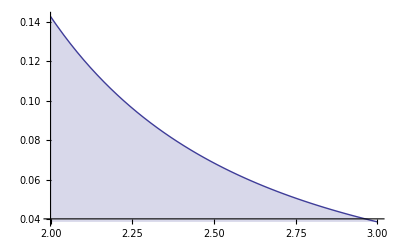

```mathematica
Plot[f[x],{x,2,3}, Filling-> Bottom]
```

Question 3: Estimate the integral using the trapaziod rule and n=5

```mathematica
N[1/5]
```

0.2

```mathematica
h[x_]=1/(-1+(x+1)^3)
```

1/(-1+(1+x)^3)

```mathematica
(1/10)*Sum[f[x]+h[x],{x,2,3,0.2}]
```

0.0623387

Question 4a: Estimate the integral with the Simpsons rule with n=10

```mathematica
(1/30)*(f[2]+f[3]+(4*Sum[f[x],{x,2.1,2.9,0.2}])+(2*Sum[f[x],{x,2.2,2.8,0.2}]))
```

0.0753903

Question 4b: Estimate the integral with the Simpsons rule with n=20

```mathematica
N[1/20]
```

0.05

```mathematica
(1/60)*(f[2]+f[3]+(4*Sum[f[x],{x,2.05,2.95,0.1}])+(2*Sum[f[x],{x,2.1,2.9,0.1}]))
```

0.0753894

Question 4c: Estimate the integral with Simpsons rule with n=40

```mathematica
N[1/40]
```

0.025

```mathematica
(1/120)*(f[2]+f[3]+(4*Sum[f[x],{x,2.025,2.975,0.05}])+(2*Sum[f[x],{x,2.05,2.95,0.05}]))
```

```mathematica
0.0753893549671799`16
```

0.0753893549671799

Below Work Done to Check for Correctness:

```mathematica
Integrate[f[x],{x,2,3}]
```

1/6 (2 √3 ArcTan[5/(√3)]-2 √3 ArcTan[7/(√3)]+Log[28/13])

```mathematica
N[1/6 (2 √3 ArcTan[5/(√3)]-2 √3 ArcTan[7/(√3)]+Log[28/13])]
```

```mathematica
0.07538935102320451`16
```

0.07538935102320451